```mathematica
cmDisp=ao==√((6/5 R -cott)/(-(1/36036 cott^3-7743/2240 cott)))
```

ao==√((-cott+(6 R)/5)/((7743 cott)/2240-cott^3/36036))

```mathematica
cmDispPWL=cmDisp//.{cott->(R/(3 Fr^2)), ao->(1/cott (2 π)/lambda)}//Simplify
```

12 √1001 √((Fr^4 (-5+18 Fr^2))/(89687169 Fr^4-80 R^2))==(Fr^2 π)/(lambda R)

```mathematica
NSolve[cmDispPWL/.{lambda->4.716, Fr->1.0}, R]
```

{{R→4.60858}}

```mathematica
Solve[cmDispPWL, R] // FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{R→-(9 √1107249 Fr^2 π)/(4 √(9009 (-5+18 Fr^2) lambda^2+5 π^2))},{R→(9 √1107249 Fr^2 π)/(4 √(9009 (-5+18 Fr^2) lambda^2+5 π^2))}}

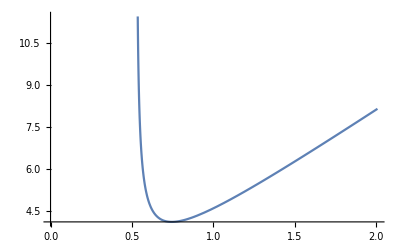

```mathematica
Plot[((9 √1107249 Fr^2 π)/(4 √(9009 (-5+18 Fr^2) lambda^2+5 π^2)))/.{lambda->4.716}, {Fr,0,2.01}]
```

```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

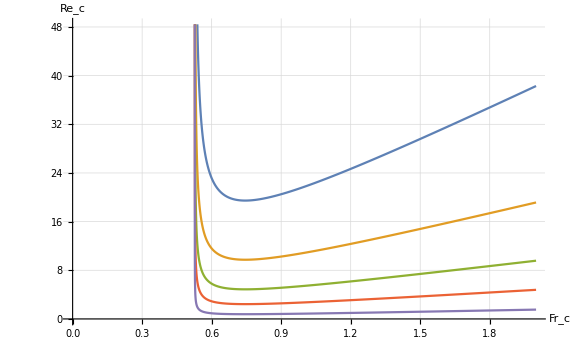

```mathematica
Plot[{((9 √1107249 Fr^2 π)/(4 √(9009 (-5+18 Fr^2) lambda^2+5 π^2)))/.{lambda->1.0}, ((9 √1107249 Fr^2 π)/(4 √(9009 (-5+18 Fr^2) lambda^2+5 π^2)))/.{lambda->2.0}, ((9 √1107249 Fr^2 π)/(4 √(9009 (-5+18 Fr^2) lambda^2+5 π^2)))/.{lambda->4.0}, ((9 √1107249 Fr^2 π)/(4 √(9009 (-5+18 Fr^2) lambda^2+5 π^2)))/.{lambda->8.0}, ((9 √1107249 Fr^2 π)/(4 √(9009 (-5+18 Fr^2) lambda^2+5 π^2)))/.{lambda->25.0}}, {Fr,0,2},GridLines->Automatic, AxesLabel->{Style["Fr_c",21,FontFamily->"Times"],Style["Re_c", 21,FontFamily->"Times"]}, PlotLegends->{MaTeX["S_o\lambda/H=1",Magnification->1.6],MaTeX["S_o\lambda/H=2",Magnification->1.6], MaTeX["S_o\lambda/H=4",Magnification->1.6], MaTeX["S_o\lambda/H=8",Magnification->1.6], MaTeX["S_o\lambda/H=25",Magnification->1.6]},PlotRange->{{0,2},{0,Automatic}}, ImageSize->Large, PlotPoints->120,TicksStyle->{{FontSize->17,FontFamily->"Times"},{FontSize->17,FontFamily->"Times"}}]
```

```mathematica
cmDispST=ao==√((6/5 R -cott)/(-(-γ c +1/36036 cott^3-7743/2240 cott)))
```

ao==√((-cott+(6 R)/5)/((7743 cott)/2240-cott^3/36036+c γ))

```mathematica
cmDispPWLST=cmDispST//.{cott->(R/(3 Fr^2)), ao->(1/cott (2 π)/lambda)}//Simplify
```

(6 Fr^2 π)/(lambda R)==√(((6/5-1/(3 Fr^2)) R)/((2581 R)/(2240 Fr^2)-R^3/(972972 Fr^6)+c γ))

```mathematica
Solve[cmDispPWLST, R] // FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{R→(3 429^(1/3) π^(2/3) (7743 143^(1/3) Fr^4 π^(2/3)+(3^(1/3) (4480 c Fr^6 (9009 (-5+18 Fr^2) lambda^2+5 π^2)^2 γ+√(Fr^12 (9009 (-5+18 Fr^2) lambda^2+5 π^2)^3 (-22128020267067 π^2+20070400 c^2 (9009 (-5+18 Fr^2) lambda^2+5 π^2) γ^2)))^(2/3))/(9009 (-5+18 Fr^2) lambda^2+5 π^2)))/(4 (4480 c Fr^6 (9009 (-5+18 Fr^2) lambda^2+5 π^2)^2 γ+√(Fr^12 (9009 (-5+18 Fr^2) lambda^2+5 π^2)^3 (-22128020267067 π^2+20070400 c^2 (9009 (-5+18 Fr^2) lambda^2+5 π^2) γ^2)))^(1/3))},{R→(46458 (-3)^(1/3) 143^(2/3) Fr^4 π^(4/3) (-9009 (-5+18 Fr^2) lambda^2-5 π^2)-3 3^(1/6) 143^(1/3) (-3 ⅈ+√3) π^(2/3) (4480 c Fr^6 (9009 (-5+18 Fr^2) lambda^2+5 π^2)^2 γ+√(Fr^12 (9009 (-5+18 Fr^2) lambda^2+5 π^2)^3 (-22128020267067 π^2+20070400 c^2 (9009 (-5+18 Fr^2) lambda^2+5 π^2) γ^2)))^(2/3))/(8 (9009 (-5+18 Fr^2) lambda^2+5 π^2) (4480 c Fr^6 (9009 (-5+18 Fr^2) lambda^2+5 π^2)^2 γ+√(Fr^12 (9009 (-5+18 Fr^2) lambda^2+5 π^2)^3 (-22128020267067 π^2+20070400 c^2 (9009 (-5+18 Fr^2) lambda^2+5 π^2) γ^2)))^(1/3))},{R→(3 3^(1/6) 143^(1/3) π^(2/3) (15486 3^(1/6) 143^(1/3) Fr^4 (9009 (-5+18 Fr^2) lambda^2 (-π)^(2/3)+5 (-1)^(2/3) π^(8/3))-(3 ⅈ+√3) (4480 c Fr^6 (9009 (-5+18 Fr^2) lambda^2+5 π^2)^2 γ+√(Fr^12 (9009 (-5+18 Fr^2) lambda^2+5 π^2)^3 (-22128020267067 π^2+20070400 c^2 (9009 (-5+18 Fr^2) lambda^2+5 π^2) γ^2)))^(2/3)))/(8 (9009 (-5+18 Fr^2) lambda^2+5 π^2) (4480 c Fr^6 (9009 (-5+18 Fr^2) lambda^2+5 π^2)^2 γ+√(Fr^12 (9009 (-5+18 Fr^2) lambda^2+5 π^2)^3 (-22128020267067 π^2+20070400 c^2 (9009 (-5+18 Fr^2) lambda^2+5 π^2) γ^2)))^(1/3))}}

```mathematica
NSolve[cmDispPWLST/.{lambda->4.716, Fr->1.0, c->1.0, γ->0.1}, R]
```

{{R→4.65138}}